```mathematica
(* Erzeugt die rekursiv definierten cardinal Bsplines aus dem 2. paper von Darden et. al.*)
```

```mathematica
M[x_, 1] := Piecewise[{{1, 0≤x≤1}}];
M[x_, p_]:=BSplineBasis[p-1,x/p];
```

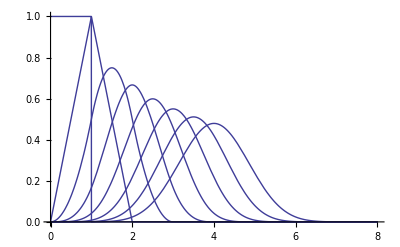

```mathematica
Plot[Table[M[x,p], {p, 1,8}], {x,0,8},PlotRange->Full ]
```

```mathematica
Print["  switch(p){"];
For[p=1, p≤16, p++,
Print["    case ", p ,": switch(i) {"];
(*For[i=0,i<p, i++,*)
For[i=0,i<p, i++,
(* pick up the polynomial of the current interval *)
h[x_]=Simplify[PiecewiseExpand[M[x+i+1/2,p]], Assumptions->-1/2≤x≤ 1/2];
If[p≥4,
h[x_]=Together[h[x]]; h[x_] = HornerForm[Numerator[h[x]] ] /Denominator[h[x]],
];
code=CForm[h[x]];
(* Avoid the use of Mathematicas Power function *)
If[p<4,
code=StringReplace[ToString[code], "Power("->"PNFFT_SQR("];
code=StringReplace[ToString[code], ",2)"->")"],
(*else*)
code=StringReplace[ToString[code], "Power(x,2)"->"x*x"];
];
(*Print["      case ", i, " : return ", code, ";"]; *)
(* P3M uses reverse index order:*)
Print["      case ", p-1-i, " : return ", code, ";"];
]
Print["      default: return 0.0;"];
  Print["    }"];
]
Print["    default: return 0.0;"];
Print["  }"];
```

switch(p){

case 1: switch(i) {

case 0 : return 1;

default: return 0.0;

}

case 2: switch(i) {

case 0 : return 0.5 + x;

case 1 : return 0.5 - x;

default: return 0.0;

}

case 3: switch(i) {

case 0 : return PNFFT_SQR(1 + 2*x)/8.;

case 1 : return 0.75 - PNFFT_SQR(x);

case 2 : return PNFFT_SQR(1 - 2*x)/8.;

default: return 0.0;

}

case 4: switch(i) {

case 0 : return (1 + x*(6 + x*(12 + 8*x)))/48.;

case 1 : return (23 + x*(30 + (-12 - 24*x)*x))/48.;

case 2 : return (23 + x*(-30 + x*(-12 + 24*x)))/48.;

case 3 : return (1 + x*(-6 + (12 - 8*x)*x))/48.;

default: return 0.0;

}

case 5: switch(i) {

case 0 : return (1 + x*(8 + x*(24 + x*(32 + 16*x))))/384.;

case 1 : return (19 + x*(44 + x*(24 + (-16 - 16*x)*x)))/96.;

case 2 : return (115 + x*x*(-120 + 48*x*x))/192.;

case 3 : return (19 + x*(-44 + x*(24 + (16 - 16*x)*x)))/96.;

case 4 : return (1 + x*(-8 + x*(24 + x*(-32 + 16*x))))/384.;

default: return 0.0;

}

case 6: switch(i) {

case 0 : return (1 + x*(10 + x*(40 + x*(80 + x*(80 + 32*x)))))/3840.;

case 1 : return (237 + x*(750 + x*(840 + x*(240 + (-240 - 160*x)*x))))/3840.;

case 2 : return (841 + x*(770 + x*(-440 + x*(-560 + x*(80 + 160*x)))))/1920.;

case 3 : return (841 + x*(-770 + x*(-440 + x*(560 + (80 - 160*x)*x))))/1920.;

case 4 : return (237 + x*(-750 + x*(840 + x*(-240 + x*(-240 + 160*x)))))/3840.;

case 5 : return (1 + x*(-10 + x*(40 + x*(-80 + (80 - 32*x)*x))))/3840.;

default: return 0.0;

}

case 7: switch(i) {

case 0 : return (1 + x*(12 + x*(60 + x*(160 + x*(240 + x*(192 + 64*x))))))/46080.;

case 1 : return (361 + x*(1416 + x*(2220 + x*(1600 + x*(240 + (-384 - 192*x)*x)))))/23040.;

case 2 : return (10543 + x*(17340 + x*(4740 + x*(-6880 + x*(-4080 + x*(960 + 960*x))))))/46080.;

case 3 : return (5887 + x*x*(-4620 + x*x*(1680 - 320*x*x)))/11520.;

case 4 : return (10543 + x*(-17340 + x*(4740 + x*(6880 + x*(-4080 + x*(-960 + 960*x))))))/46080.;

case 5 : return (361 + x*(-1416 + x*(2220 + x*(-1600 + x*(240 + (384 - 192*x)*x)))))/23040.;

case 6 : return (1 + x*(-12 + x*(60 + x*(-160 + x*(240 + x*(-192 + 64*x))))))/46080.;

default: return 0.0;

}

case 8: switch(i) {

case 0 : return (1 + x*(14 + x*(84 + x*(280 + x*(560 + x*(672 + x*(448 + 128*x)))))))/645120.;

case 1 : return (2179 + x*(10094 + x*(19740 + x*(20440 + x*(10640 + x*(672 + (-2240 - 896*x)*x))))))/645120.;

case 2 : return (60657 + x*(137494 + x*(101556 + x*(1400 + x*(-35280 + x*(-12768 + x*(4032 + 2688*x)))))))/645120.;

case 3 : return (259723 + x*(182070 + x*(-121380 + x*(-108360 + x*(24080 + x*(30240 + (-2240 - 4480*x)*x))))))/645120.;

case 4 : return (259723 + x*(-182070 + x*(-121380 + x*(108360 + x*(24080 + x*(-30240 + x*(-2240 + 4480*x)))))))/645120.;

case 5 : return (60657 + x*(-137494 + x*(101556 + x*(-1400 + x*(-35280 + x*(12768 + (4032 - 2688*x)*x))))))/645120.;

case 6 : return (2179 + x*(-10094 + x*(19740 + x*(-20440 + x*(10640 + x*(-672 + x*(-2240 + 896*x)))))))/645120.;

case 7 : return (1 + x*(-14 + x*(84 + x*(-280 + x*(560 + x*(-672 + (448 - 128*x)*x))))))/645120.;

default: return 0.0;

}

case 9: switch(i) {

case 0 : return (1 + x*(16 + x*(112 + x*(448 + x*(1120 + x*(1792 + x*(1792 + x*(1024 + 256*x))))))))/1.032192e7;

case 1 : return (819 + x*(4356 + x*(10080 + x*(13104 + x*(10080 + x*(4032 + (-768 - 256*x)*x*x))))))/1.29024e6;

case 2 : return (82903 + x*(233912 + x*(254800 + x*(109088 + x*(-19040 + x*(-36736 + x*(-8960 + x*(3584 + 1792*x))))))))/2.58048e6;

case 3 : return (310661 + x*(398132 + x*(44576 + x*(-148624 + x*(-54880 + x*(23744 + x*(14336 + (-1792 - 1792*x)*x)))))))/1.29024e6;

case 4 : return (2337507 + x*x*(-1456560 + x*x*(433440 + x*x*(-80640 + 8960*x*x))))/5.16096e6;

case 5 : return (310661 + x*(-398132 + x*(44576 + x*(148624 + x*(-54880 + x*(-23744 + x*(14336 + (1792 - 1792*x)*x)))))))/1.29024e6;

case 6 : return (82903 + x*(-233912 + x*(254800 + x*(-109088 + x*(-19040 + x*(36736 + x*(-8960 + x*(-3584 + 1792*x))))))))/2.58048e6;

case 7 : return (819 + x*(-4356 + x*(10080 + x*(-13104 + x*(10080 + x*(-4032 + (768 - 256*x)*x*x))))))/1.29024e6;

case 8 : return (1 + x*(-16 + x*(112 + x*(-448 + x*(1120 + x*(-1792 + x*(1792 + x*(-1024 + 256*x))))))))/1.032192e7;

default: return 0.0;

}

case 10: switch(i) {

case 0 : return (1 + x*(18 + x*(144 + x*(672 + x*(2016 + x*(4032 + x*(5376 + x*(4608 + x*(2304 + 512*x)))))))))/1.8579456e8;

case 1 : return (19673 + x*(117918 + x*(313488 + x*(483168 + x*(469728 + x*(286272 + x*(91392 + x*(-4608 + (-16128 - 4608*x)*x))))))))/1.8579456e8;

case 2 : return (439085 + x*(1462770 + x*(2026800 + x*(1407840 + x*(372960 + x*(-141120 + x*(-134400 + x*(-23040 + x*(11520 + 4608*x)))))))))/4.644864e7;

case 3 : return (5426993 + x*(9691542 + x*(5061168 + x*(-993888 + x*(-1828512 + x*(-326592 + x*(252672 + x*(96768 + (-16128 - 10752*x)*x))))))))/4.644864e7;

case 4 : return (34706647 + x*(19707534 + x*(-14332752 + x*(-9809184 + x*(2675232 + x*(2350656 + x*(-284928 + x*(-354816 + x*(16128 + 32256*x)))))))))/9.289728e7;

case 5 : return (34706647 + x*(-19707534 + x*(-14332752 + x*(9809184 + x*(2675232 + x*(-2350656 + x*(-284928 + x*(354816 + (16128 - 32256*x)*x))))))))/9.289728e7;

case 6 : return (5426993 + x*(-9691542 + x*(5061168 + x*(993888 + x*(-1828512 + x*(326592 + x*(252672 + x*(-96768 + x*(-16128 + 10752*x)))))))))/4.644864e7;

case 7 : return (439085 + x*(-1462770 + x*(2026800 + x*(-1407840 + x*(372960 + x*(141120 + x*(-134400 + x*(23040 + (11520 - 4608*x)*x))))))))/4.644864e7;

case 8 : return (19673 + x*(-117918 + x*(313488 + x*(-483168 + x*(469728 + x*(-286272 + x*(91392 + x*(4608 + x*(-16128 + 4608*x)))))))))/1.8579456e8;

case 9 : return (1 + x*(-18 + x*(144 + x*(-672 + x*(2016 + x*(-4032 + x*(5376 + x*(-4608 + (2304 - 512*x)*x))))))))/1.8579456e8;

default: return 0.0;

}

case 11: switch(i) {

case 0 : return (1 + x*(20 + x*(180 + x*(960 + x*(3360 + x*(8064 + x*(13440 + x*(15360 + x*(11520 + x*(5120 + 1024*x))))))))))/3.7158912e9;

case 1 : return (29519 + x*(196720 + x*(589500 + x*(1044480 + x*(1206240 + x*(935424 + x*(470400 + x*(122880 + x*(-11520 + (-20480 - 5120*x)*x)))))))))/1.8579456e9;

case 2 : return (9116141 + x*(34733340 + x*(57331620 + x*(51958080 + x*(25740960 + x*(4088448 + x*(-2835840 + x*(-1797120 + x*(-218880 + x*(138240 + 46080*x))))))))))/3.7158912e9;

case 3 : return (22287613 + x*(49879080 + x*(41143860 + x*(10114560 + x*(-6004320 + x*(-4402944 + x*(-309120 + x*(552960 + x*(149760 + (-30720 - 15360*x)*x)))))))))/4.644864e8;

case 4 : return (453461641 + x*(477053220 + x*(3244500 + x*(-163033920 + x*(-39107040 + x*(25329024 + x*(10012800 + x*(-2257920 + x*(-1370880 + x*(107520 + 107520*x))))))))))/1.8579456e9;

case 5 : return (381773117 + x*x*(-197075340 + x*x*(49045920 + x*x*(-7835520 + x*x*(887040 - 64512*x*x)))))/9.289728e8;

case 6 : return (453461641 + x*(-477053220 + x*(3244500 + x*(163033920 + x*(-39107040 + x*(-25329024 + x*(10012800 + x*(2257920 + x*(-1370880 + x*(-107520 + 107520*x))))))))))/1.8579456e9;

case 7 : return (22287613 + x*(-49879080 + x*(41143860 + x*(-10114560 + x*(-6004320 + x*(4402944 + x*(-309120 + x*(-552960 + x*(149760 + (30720 - 15360*x)*x)))))))))/4.644864e8;

case 8 : return (9116141 + x*(-34733340 + x*(57331620 + x*(-51958080 + x*(25740960 + x*(-4088448 + x*(-2835840 + x*(1797120 + x*(-218880 + x*(-138240 + 46080*x))))))))))/3.7158912e9;

case 9 : return (29519 + x*(-196720 + x*(589500 + x*(-1044480 + x*(1206240 + x*(-935424 + x*(470400 + x*(-122880 + x*(-11520 + (20480 - 5120*x)*x)))))))))/1.8579456e9;

case 10 : return (1 + x*(-20 + x*(180 + x*(-960 + x*(3360 + x*(-8064 + x*(13440 + x*(-15360 + x*(11520 + x*(-5120 + 1024*x))))))))))/3.7158912e9;

default: return 0.0;

}

case 12: switch(i) {

case 0 : return (1 + x*(22 + x*(220 + x*(1320 + x*(5280 + x*(14784 + x*(29568 + x*(42240 + x*(42240 + x*(28160 + x*(11264 + 2048*x)))))))))))/8.17496064e10;

case 1 : return (177135 + x*(1298814 + x*(4327620 + x*(8644680 + x*(11484000 + x*(10600128 + x*(6830208 + x*(2914560 + x*(633600 + x*(-84480 + (-101376 - 22528*x)*x))))))))))/8.17496064e10;

case 2 : return (46702427 + x*(199256266 + x*(377738900 + x*(411785880 + x*(274280160 + x*(102645312 + x*(8131200 + x*(-11869440 + x*(-5617920 + x*(-478720 + x*(394240 + 112640*x)))))))))))/8.17496064e10;

case 3 : return (467693575 + x*(1240688262 + x*(1335764100 + x*(664447080 + x*(53090400 + x*(-108204096 + x*(-48048000 + x*(380160 + x*(5702400 + x*(1154560 + (-281600 - 112640*x)*x))))))))))/2.72498688e10;

case 4 : return (1806137183 + x*(2671615386 + x*(1017635300 + x*(-394364520 + x*(-373068960 + x*(-22131648 + x*(52483200 + x*(11784960 + x*(-4097280 + x*(-1605120 + x*(168960 + 112640*x)))))))))))/1.36249344e10;

case 5 : return (4764669969 + x*(2273953682 + x*(-1749195140 + x*(-971410440 + x*(298895520 + x*(201225024 + x*(-30957696 + x*(-26906880 + x*(2069760 + x*(2562560 + (-78848 - 157696*x)*x))))))))))/1.36249344e10;

case 6 : return (4764669969 + x*(-2273953682 + x*(-1749195140 + x*(971410440 + x*(298895520 + x*(-201225024 + x*(-30957696 + x*(26906880 + x*(2069760 + x*(-2562560 + x*(-78848 + 157696*x)))))))))))/1.36249344e10;

case 7 : return (1806137183 + x*(-2671615386 + x*(1017635300 + x*(394364520 + x*(-373068960 + x*(22131648 + x*(52483200 + x*(-11784960 + x*(-4097280 + x*(1605120 + (168960 - 112640*x)*x))))))))))/1.36249344e10;

case 8 : return (467693575 + x*(-1240688262 + x*(1335764100 + x*(-664447080 + x*(53090400 + x*(108204096 + x*(-48048000 + x*(-380160 + x*(5702400 + x*(-1154560 + x*(-281600 + 112640*x)))))))))))/2.72498688e10;

case 9 : return (46702427 + x*(-199256266 + x*(377738900 + x*(-411785880 + x*(274280160 + x*(-102645312 + x*(8131200 + x*(11869440 + x*(-5617920 + x*(478720 + (394240 - 112640*x)*x))))))))))/8.17496064e10;

case 10 : return (177135 + x*(-1298814 + x*(4327620 + x*(-8644680 + x*(11484000 + x*(-10600128 + x*(6830208 + x*(-2914560 + x*(633600 + x*(84480 + x*(-101376 + 22528*x)))))))))))/8.17496064e10;

case 11 : return (1 + x*(-22 + x*(220 + x*(-1320 + x*(5280 + x*(-14784 + x*(29568 + x*(-42240 + x*(42240 + x*(-28160 + (11264 - 2048*x)*x))))))))))/8.17496064e10;

default: return 0.0;

}

case 13: switch(i) {

case 0 : return (1 + x*(24 + x*(264 + x*(1760 + x*(7920 + x*(25344 + x*(59136 + x*(101376 + x*(126720 + x*(112640 + x*(67584 + x*(24576 + 4096*x))))))))))))/1.9619905536e12;

case 1 : return (132857 + x*(1062804 + x*(3896376 + x*(8654800 + x*(12965040 + x*(13774464 + x*(10585344 + x*(5829120 + x*(2154240 + x*(394240 + x*(-67584 + (-61440 - 12288*x)*x)))))))))))/4.904976384e11;

case 2 : return (118615985 + x*(558303504 + x*(1187744712 + x*(1493645120 + x*(1209423600 + x*(630710784 + x*(184090368 + x*(2230272 + x*(-22176000 + x*(-8335360 + x*(-473088 + x*(540672 + 135168*x))))))))))))/9.809952768e11;

case 3 : return (2677227797 + x*(8138269788 + x*(10568425560 + x*(7259106800 + x*(2372333040 + x*(-138010752 + x*(-427257600 + x*(-130521600 + x*(9757440 + x*(15150080 + x*(2365440 + (-675840 - 225280*x)*x)))))))))))/4.904976384e11;

case 4 : return (40461260069 + x*(75469938984 + x*(49230510120 + x*(5596052000 + x*(-8719056720 + x*(-3836295936 + x*(255763200 + x*(524620800 + x*(69569280 + x*(-37058560 + x*(-10475520 + x*(1351680 + 675840*x))))))))))))/6.539968512e11;

case 5 : return (19875856851 + x*(17751196716 + x*(-1192985112 + x*(-5533660880 + x*(-865568880 + x*(806357376 + x*(223356672 + x*(-71520768 + x*(-29018880 + x*(4111360 + x*(2500608 + (-135168 - 135168*x)*x)))))))))))/8.17496064e10;

case 6 : return (61940709597 + x*x*(-27287444184 + x*x*(5828462640 + x*x*(-804900096 + x*x*(80720640 + x*x*(-6150144 + 315392*x*x))))))/1.634992128e11;

case 7 : return (19875856851 + x*(-17751196716 + x*(-1192985112 + x*(5533660880 + x*(-865568880 + x*(-806357376 + x*(223356672 + x*(71520768 + x*(-29018880 + x*(-4111360 + x*(2500608 + (135168 - 135168*x)*x)))))))))))/8.17496064e10;

case 8 : return (40461260069 + x*(-75469938984 + x*(49230510120 + x*(-5596052000 + x*(-8719056720 + x*(3836295936 + x*(255763200 + x*(-524620800 + x*(69569280 + x*(37058560 + x*(-10475520 + x*(-1351680 + 675840*x))))))))))))/6.539968512e11;

case 9 : return (2677227797 + x*(-8138269788 + x*(10568425560 + x*(-7259106800 + x*(2372333040 + x*(138010752 + x*(-427257600 + x*(130521600 + x*(9757440 + x*(-15150080 + x*(2365440 + (675840 - 225280*x)*x)))))))))))/4.904976384e11;

case 10 : return (118615985 + x*(-558303504 + x*(1187744712 + x*(-1493645120 + x*(1209423600 + x*(-630710784 + x*(184090368 + x*(-2230272 + x*(-22176000 + x*(8335360 + x*(-473088 + x*(-540672 + 135168*x))))))))))))/9.809952768e11;

case 11 : return (132857 + x*(-1062804 + x*(3896376 + x*(-8654800 + x*(12965040 + x*(-13774464 + x*(10585344 + x*(-5829120 + x*(2154240 + x*(-394240 + x*(-67584 + (61440 - 12288*x)*x)))))))))))/4.904976384e11;

case 12 : return (1 + x*(-24 + x*(264 + x*(-1760 + x*(7920 + x*(-25344 + x*(59136 + x*(-101376 + x*(126720 + x*(-112640 + x*(67584 + x*(-24576 + 4096*x))))))))))))/1.9619905536e12;

default: return 0.0;

}

case 14: switch(i) {

case 0 : return (1 + x*(26 + x*(312 + x*(2288 + x*(11440 + x*(41184 + x*(109824 + x*(219648 + x*(329472 + x*(366080 + x*(292864 + x*(159744 + x*(53248 + 8192*x)))))))))))))/5.10117543936e13;

case 1 : return (1594309 + x*(13817102 + x*(55265496 + x*(135072080 + x*(225013360 + x*(269631648 + x*(238647552 + x*(157048320 + x*(75449088 + x*(24527360 + x*(3807232 + x*(-798720 + (-585728 - 106496*x)*x))))))))))))/5.10117543936e13;

case 2 : return (599191347 + x*(3077107046 + x*(7230312648 + x*(10226250320 + x*(9596180880 + x*(6154166304 + x*(2613701376 + x*(605130240 + x*(-30640896 + x*(-76510720 + x*(-23721984 + x*(-798720 + x*(1437696 + 319488*x)))))))))))))/2.55058771968e13;

case 3 : return (39972124843 + x*(136131829834 + x*(204337068936 + x*(172892255536 + x*(84659695120 + x*(18383260896 + x*(-3929173248 + x*(-3857677824 + x*(-855638784 + x*(120440320 + x*(100452352 + x*(12300288 + (-4100096 - 1171456*x)*x))))))))))))/2.55058771968e13;

case 4 : return (1295923334435 + x*(2877546594494 + x*(2520137591400 + x*(913621177040 + x*(-79613762800 + x*(-185361812064 + x*(-47479660800 + x*(9197760000 + x*(6811833600 + x*(490181120 + x*(-446617600 + x*(-96645120 + x*(14643200 + 5857280*x)))))))))))))/5.10117543936e13;

case 5 : return (2436916824061 + x*(3082185463214 + x*(865015251672 + x*(-509378055472 + x*(-324124703760 + x*(9331429536 + x*(44577671424 + x*(5686906368 + x*(-3564557568 + x*(-871636480 + x*(181868544 + x*(72044544 + (-5271552 - 3514368*x)*x))))))))))))/1.70039181312e13;

case 6 : return (1401504930291 + x*(576913893270 + x*(-461531114616 + x*(-215812774320 + x*(71937591440 + x*(39309922080 + x*(-6988430592 + x*(-4648849920 + x*(464884992 + x*(400857600 + x*(-21379072 + x*(-26357760 + x*(585728 + 1171456*x)))))))))))))/4.2509795328e12;

case 7 : return (1401504930291 + x*(-576913893270 + x*(-461531114616 + x*(215812774320 + x*(71937591440 + x*(-39309922080 + x*(-6988430592 + x*(4648849920 + x*(464884992 + x*(-400857600 + x*(-21379072 + x*(26357760 + (585728 - 1171456*x)*x))))))))))))/4.2509795328e12;

case 8 : return (2436916824061 + x*(-3082185463214 + x*(865015251672 + x*(509378055472 + x*(-324124703760 + x*(-9331429536 + x*(44577671424 + x*(-5686906368 + x*(-3564557568 + x*(871636480 + x*(181868544 + x*(-72044544 + x*(-5271552 + 3514368*x)))))))))))))/1.70039181312e13;

case 9 : return (1295923334435 + x*(-2877546594494 + x*(2520137591400 + x*(-913621177040 + x*(-79613762800 + x*(185361812064 + x*(-47479660800 + x*(-9197760000 + x*(6811833600 + x*(-490181120 + x*(-446617600 + x*(96645120 + (14643200 - 5857280*x)*x))))))))))))/5.10117543936e13;

case 10 : return (39972124843 + x*(-136131829834 + x*(204337068936 + x*(-172892255536 + x*(84659695120 + x*(-18383260896 + x*(-3929173248 + x*(3857677824 + x*(-855638784 + x*(-120440320 + x*(100452352 + x*(-12300288 + x*(-4100096 + 1171456*x)))))))))))))/2.55058771968e13;

case 11 : return (599191347 + x*(-3077107046 + x*(7230312648 + x*(-10226250320 + x*(9596180880 + x*(-6154166304 + x*(2613701376 + x*(-605130240 + x*(-30640896 + x*(76510720 + x*(-23721984 + x*(798720 + (1437696 - 319488*x)*x))))))))))))/2.55058771968e13;

case 12 : return (1594309 + x*(-13817102 + x*(55265496 + x*(-135072080 + x*(225013360 + x*(-269631648 + x*(238647552 + x*(-157048320 + x*(75449088 + x*(-24527360 + x*(3807232 + x*(798720 + x*(-585728 + 106496*x)))))))))))))/5.10117543936e13;

case 13 : return (1 + x*(-26 + x*(312 + x*(-2288 + x*(11440 + x*(-41184 + x*(109824 + x*(-219648 + x*(329472 + x*(-366080 + x*(292864 + x*(-159744 + (53248 - 8192*x)*x))))))))))))/5.10117543936e13;

default: return 0.0;

}

case 15: switch(i) {

case 0 : return (1 + x*(28 + x*(364 + x*(2912 + x*(16016 + x*(64064 + x*(192192 + x*(439296 + x*(768768 + x*(1025024 + x*(1025024 + x*(745472 + x*(372736 + x*(114688 + 16384*x))))))))))))))/1.4283291230208e15;

case 1 : return (2391477 + x*(22320312 + x*(96719532 + x*(257904192 + x*(472744272 + x*(630005376 + x*(629044416 + x*(477075456 + x*(274450176 + x*(116852736 + x*(33825792 + x*(4472832 + x*(-1118208 + (-688128 - 114688*x)*x)))))))))))))/7.141645615104e14;

case 2 : return (6031771195 + x*(33510074780 + x*(85965557860 + x*(134450024800 + x*(142221999920 + x*(106217151040 + x*(56180604480 + x*(19955020800 + x*(3686242560 + x*(-425384960 + x*(-497136640 + x*(-130457600 + x*(-1863680 + x*(7454720 + 1490944*x))))))))))))))/1.4283291230208e15;

case 3 : return (146793137441 + x*(551221068944 + x*(931383059516 + x*(919831529344 + x*(569331018256 + x*(210177839872 + x*(28534554048 + x*(-13085749248 + x*(-7809914112 + x*(-1283330048 + x*(275731456 + x*(158040064 + x*(15282176 + (-5963776 - 1490944*x)*x)))))))))))))/3.570822807552e14;

case 4 : return (13342139253321 + x*(34047414372972 + x*(36473961087564 + x*(19706992232928 + x*(3974856661776 + x*(-1394025657024 + x*(-1036598891328 + x*(-158485257216 + x*(59195904768 + x*(26516345856 + x*(698041344 + x*(-1648238592 + x*(-282906624 + x*(49201152 + 16400384*x))))))))))))))/1.4283291230208e15;

case 5 : return (52520399274139 + x*(84207579928472 + x*(44583068566036 + x*(349571430208 + x*(-8546143702096 + x*(-2499728975744 + x*(497830901568 + x*(362425350144 + x*(13760178432 + x*(-27230787584 + x*(-4347126784 + x*(1262829568 + x*(364908544 + (-32800768 - 16400384*x)*x)))))))))))))/7.141645615104e14;

case 6 : return (114305842384169 + x*(88734881118884 + x*(-10843418461876 + x*(-25303970627936 + x*(-2477111292656 + x*(3426500389312 + x*(690238540992 + x*(-290125575168 + x*(-84988071168 + x*(16874970112 + x*(6930187264 + x*(-680615936 + x*(-414109696 + x*(16400384 + 16400384*x))))))))))))))/4.761097076736e14;

case 7 : return (21022573954365 + x*x*(-8076794505780 + x*x*(1510689420240 + x*x*(-183446303040 + x*x*(16270974720 + x*x*(-1122401280 + x*x*(61501440 - 2342912*x*x)))))))/5.95137134592e13;

case 8 : return (114305842384169 + x*(-88734881118884 + x*(-10843418461876 + x*(25303970627936 + x*(-2477111292656 + x*(-3426500389312 + x*(690238540992 + x*(290125575168 + x*(-84988071168 + x*(-16874970112 + x*(6930187264 + x*(680615936 + x*(-414109696 + x*(-16400384 + 16400384*x))))))))))))))/4.761097076736e14;

case 9 : return (52520399274139 + x*(-84207579928472 + x*(44583068566036 + x*(-349571430208 + x*(-8546143702096 + x*(2499728975744 + x*(497830901568 + x*(-362425350144 + x*(13760178432 + x*(27230787584 + x*(-4347126784 + x*(-1262829568 + x*(364908544 + (32800768 - 16400384*x)*x)))))))))))))/7.141645615104e14;

case 10 : return (13342139253321 + x*(-34047414372972 + x*(36473961087564 + x*(-19706992232928 + x*(3974856661776 + x*(1394025657024 + x*(-1036598891328 + x*(158485257216 + x*(59195904768 + x*(-26516345856 + x*(698041344 + x*(1648238592 + x*(-282906624 + x*(-49201152 + 16400384*x))))))))))))))/1.4283291230208e15;

case 11 : return (146793137441 + x*(-551221068944 + x*(931383059516 + x*(-919831529344 + x*(569331018256 + x*(-210177839872 + x*(28534554048 + x*(13085749248 + x*(-7809914112 + x*(1283330048 + x*(275731456 + x*(-158040064 + x*(15282176 + (5963776 - 1490944*x)*x)))))))))))))/3.570822807552e14;

case 12 : return (6031771195 + x*(-33510074780 + x*(85965557860 + x*(-134450024800 + x*(142221999920 + x*(-106217151040 + x*(56180604480 + x*(-19955020800 + x*(3686242560 + x*(425384960 + x*(-497136640 + x*(130457600 + x*(-1863680 + x*(-7454720 + 1490944*x))))))))))))))/1.4283291230208e15;

case 13 : return (2391477 + x*(-22320312 + x*(96719532 + x*(-257904192 + x*(472744272 + x*(-630005376 + x*(629044416 + x*(-477075456 + x*(274450176 + x*(-116852736 + x*(33825792 + x*(-4472832 + x*(-1118208 + (688128 - 114688*x)*x)))))))))))))/7.141645615104e14;

case 14 : return (1 + x*(-28 + x*(364 + x*(-2912 + x*(16016 + x*(-64064 + x*(192192 + x*(-439296 + x*(768768 + x*(-1025024 + x*(1025024 + x*(-745472 + x*(372736 + x*(-114688 + 16384*x))))))))))))))/1.4283291230208e15;

default: return 0.0;

}

case 16: switch(i) {

case 0 : return (1 + x*(30 + x*(420 + x*(3640 + x*(21840 + x*(96096 + x*(320320 + x*(823680 + x*(1647360 + x*(2562560 + x*(3075072 + x*(2795520 + x*(1863680 + x*(860160 + x*(245760 + 32768*x)))))))))))))))/4.2849873690624e16;

case 1 : return (14348891 + x*(143488590 + x*(669608940 + x*(1934387000 + x*(3868541040 + x*(5672835168 + x*(6299733440 + x*(5390985600 + x*(3576418560 + x*(1827105280 + x*(698041344 + x*(181708800 + x*(20500480 + x*(-6021120 + (-3194880 - 491520*x)*x))))))))))))))/4.2849873690624e16;

case 2 : return (30287995733 + x*(180809647230 + x*(501981512340 + x*(857721187960 + x*(1004506623120 + x*(847659068256 + x*(524785701440 + x*(235382209920 + x*(71253262080 + x*(10457807360 + x*(-1977271296 + x*(-1540331520 + x*(-348508160 + x*(860160 + x*(18923520 + 3440640*x)))))))))))))))/4.2849873690624e16;

case 3 : return (4261002128223 + x*(17434223357070 + x*(32570613014940 + x*(36395666802040 + x*(26586570694320 + x*(12810612438624 + x*(3672471042240 + x*(248389764480 + x*(-271117566720 + x*(-116419663360 + x*(-14123805696 + x*(4363806720 + x*(1906544640 + x*(145367040 + (-67092480 - 14909440*x)*x))))))))))))))/4.2849873690624e16;

case 4 : return (133584221924461 + x*(382649001106710 + x*(477637951457940 + x*(327484288495000 + x*(120207495866640 + x*(10185195532512 + x*(-11173685082560 + x*(-4931730460800 + x*(-398033475840 + x*(301451870720 + x*(94948998144 + x*(-1104230400 + x*(-5700997120 + x*(-793927680 + x*(156549120 + 44728320*x)))))))))))))))/4.2849873690624e16;

case 5 : return (1435633708350799 + x*(2750959778848710 + x*(2015516182259580 + x*(526921760445080 + x*(-142558870293840 + x*(-126402864395808 + x*(-18027161472320 + x*(8709688690560 + x*(3312509840640 + x*(-105585159680 + x*(-242933763072 + x*(-25615349760 + x*(10434744320 + x*(2337054720 + (-246005760 - 98402304*x)*x))))))))))))))/4.2849873690624e16;

case 6 : return (6453703025399873 + x*(7136301858126870 + x*(1466842252495620 + x*(-1216963925177000 + x*(-574582910581680 + x*(57965721157344 + x*(76394795597120 + x*(4607373513600 + x*(-5982102846720 + x*(-941615234560 + x*(315259456512 + x*(80413132800 + x*(-11418767360 + x*(-4551106560 + x*(246005760 + 164003840*x)))))))))))))))/4.2849873690624e16;

case 7 : return (4465908195054673 + x*(1616242477522530 + x*(-1331023216783260 + x*(-537709375843640 + x*(189779779709520 + x*(87375759927456 + x*(-17132501946560 + x*(-9247752708480 + x*(1087970906880 + x*(717186229760 + x*(-50624910336 + x*(-43389265920 + x*(1701539840 + x*(2091048960 + (-35143680 - 70287360*x)*x))))))))))))))/1.4283291230208e16;

case 8 : return (4465908195054673 + x*(-1616242477522530 + x*(-1331023216783260 + x*(537709375843640 + x*(189779779709520 + x*(-87375759927456 + x*(-17132501946560 + x*(9247752708480 + x*(1087970906880 + x*(-717186229760 + x*(-50624910336 + x*(43389265920 + x*(1701539840 + x*(-2091048960 + x*(-35143680 + 70287360*x)))))))))))))))/1.4283291230208e16;

case 9 : return (6453703025399873 + x*(-7136301858126870 + x*(1466842252495620 + x*(1216963925177000 + x*(-574582910581680 + x*(-57965721157344 + x*(76394795597120 + x*(-4607373513600 + x*(-5982102846720 + x*(941615234560 + x*(315259456512 + x*(-80413132800 + x*(-11418767360 + x*(4551106560 + (246005760 - 164003840*x)*x))))))))))))))/4.2849873690624e16;

case 10 : return (1435633708350799 + x*(-2750959778848710 + x*(2015516182259580 + x*(-526921760445080 + x*(-142558870293840 + x*(126402864395808 + x*(-18027161472320 + x*(-8709688690560 + x*(3312509840640 + x*(105585159680 + x*(-242933763072 + x*(25615349760 + x*(10434744320 + x*(-2337054720 + x*(-246005760 + 98402304*x)))))))))))))))/4.2849873690624e16;

case 11 : return (133584221924461 + x*(-382649001106710 + x*(477637951457940 + x*(-327484288495000 + x*(120207495866640 + x*(-10185195532512 + x*(-11173685082560 + x*(4931730460800 + x*(-398033475840 + x*(-301451870720 + x*(94948998144 + x*(1104230400 + x*(-5700997120 + x*(793927680 + (156549120 - 44728320*x)*x))))))))))))))/4.2849873690624e16;

case 12 : return (4261002128223 + x*(-17434223357070 + x*(32570613014940 + x*(-36395666802040 + x*(26586570694320 + x*(-12810612438624 + x*(3672471042240 + x*(-248389764480 + x*(-271117566720 + x*(116419663360 + x*(-14123805696 + x*(-4363806720 + x*(1906544640 + x*(-145367040 + x*(-67092480 + 14909440*x)))))))))))))))/4.2849873690624e16;

case 13 : return (30287995733 + x*(-180809647230 + x*(501981512340 + x*(-857721187960 + x*(1004506623120 + x*(-847659068256 + x*(524785701440 + x*(-235382209920 + x*(71253262080 + x*(-10457807360 + x*(-1977271296 + x*(1540331520 + x*(-348508160 + x*(-860160 + (18923520 - 3440640*x)*x))))))))))))))/4.2849873690624e16;

case 14 : return (14348891 + x*(-143488590 + x*(669608940 + x*(-1934387000 + x*(3868541040 + x*(-5672835168 + x*(6299733440 + x*(-5390985600 + x*(3576418560 + x*(-1827105280 + x*(698041344 + x*(-181708800 + x*(20500480 + x*(6021120 + x*(-3194880 + 491520*x)))))))))))))))/4.2849873690624e16;

case 15 : return (1 + x*(-30 + x*(420 + x*(-3640 + x*(21840 + x*(-96096 + x*(320320 + x*(-823680 + x*(1647360 + x*(-2562560 + x*(3075072 + x*(-2795520 + x*(1863680 + x*(-860160 + (245760 - 32768*x)*x))))))))))))))/4.2849873690624e16;

default: return 0.0;

}

}

```mathematica
(* Do the same for the derivatives. *)
```

```mathematica
(*Print["  switch(p){"];
For[p=1, p≤16, p++,
If[p==1, Print["    case 1: return 0.0;"];  Continue[]];
Print["    case ", p ,": switch(i) {"];
(*For[i=0,i<p, i++,*)
For[i=0,i<p, i++,
(* pick up the polynomial of the current interval *)
h[x_]=D[Simplify[PiecewiseExpand[M[x+i+1/2,p]], Assumptions->-1/2≤x≤ 1/2], x];
If[p< 4,
h[x_]=Expand[h[x]],
(* else *)
h[x_] = Together[h[x]];
 h[x_] = HornerForm[Numerator[h[x]] ] /Denominator[h[x]];
];
code=CForm[h[x]];
(* Avoid the use of Mathematicas Power function *)
code=StringReplace[ToString[code], "Power(x,2)"->"x*x"];
(*Print["      case ", p-1-i, " : return ", code, ";"];*)
Print["      case ", i, " : return ", code, ";"];
]
Print["      default: return 0.0;"];
  Print["    }"];
]
Print["    default: return 0.0;"];
Print["  }"];*)
```

switch(p){

case 1: return 0.0;

case 2: switch(i) {

case 0 : return 1;

case 1 : return -1;

default: return 0.0;

}

case 3: switch(i) {

case 0 : return 0.5 + x;

case 1 : return -2*x;

case 2 : return -0.5 + x;

default: return 0.0;

}

case 4: switch(i) {

case 0 : return (1 + x*(4 + 4*x))/8.;

case 1 : return (5 + (-4 - 12*x)*x)/8.;

case 2 : return (-5 + x*(-4 + 12*x))/8.;

case 3 : return (-1 + (4 - 4*x)*x)/8.;

default: return 0.0;

}

case 5: switch(i) {

case 0 : return (1 + x*(6 + x*(12 + 8*x)))/48.;

case 1 : return (11 + x*(12 + (-12 - 16*x)*x))/24.;

case 2 : return (x*(-5 + 4*x*x))/4.;

case 3 : return (-11 + x*(12 + (12 - 16*x)*x))/24.;

case 4 : return (-1 + x*(6 + x*(-12 + 8*x)))/48.;

default: return 0.0;

}

case 6: switch(i) {

case 0 : return (1 + x*(8 + x*(24 + x*(32 + 16*x))))/384.;

case 1 : return (75 + x*(168 + x*(72 + (-96 - 80*x)*x)))/384.;

case 2 : return (77 + x*(-88 + x*(-168 + x*(32 + 80*x))))/192.;

case 3 : return (-77 + x*(-88 + x*(168 + (32 - 80*x)*x)))/192.;

case 4 : return (-75 + x*(168 + x*(-72 + x*(-96 + 80*x))))/384.;

case 5 : return (-1 + x*(8 + x*(-24 + (32 - 16*x)*x)))/384.;

default: return 0.0;

}

case 7: switch(i) {

case 0 : return (1 + x*(10 + x*(40 + x*(80 + x*(80 + 32*x)))))/3840.;

case 1 : return (59 + x*(185 + x*(200 + x*(40 + (-80 - 48*x)*x))))/960.;

case 2 : return (289 + x*(158 + x*(-344 + x*(-272 + x*(80 + 96*x)))))/768.;

case 3 : return (x*(-77 + x*x*(56 - 16*x*x)))/96.;

case 4 : return (-289 + x*(158 + x*(344 + x*(-272 + x*(-80 + 96*x)))))/768.;

case 5 : return (-59 + x*(185 + x*(-200 + x*(40 + (80 - 48*x)*x))))/960.;

case 6 : return (-1 + x*(10 + x*(-40 + x*(80 + x*(-80 + 32*x)))))/3840.;

default: return 0.0;

}

case 8: switch(i) {

case 0 : return (1 + x*(12 + x*(60 + x*(160 + x*(240 + x*(192 + 64*x))))))/46080.;

case 1 : return (721 + x*(2820 + x*(4380 + x*(3040 + x*(240 + (-960 - 448*x)*x)))))/46080.;

case 2 : return (9821 + x*(14508 + x*(300 + x*(-10080 + x*(-4560 + x*(1728 + 1344*x))))))/46080.;

case 3 : return (2601 + x*(-3468 + x*(-4644 + x*(1376 + x*(2160 + (-192 - 448*x)*x)))))/9216.;

case 4 : return (-2601 + x*(-3468 + x*(4644 + x*(1376 + x*(-2160 + x*(-192 + 448*x))))))/9216.;

case 5 : return (-9821 + x*(14508 + x*(-300 + x*(-10080 + x*(4560 + (1728 - 1344*x)*x)))))/46080.;

case 6 : return (-721 + x*(2820 + x*(-4380 + x*(3040 + x*(-240 + x*(-960 + 448*x))))))/46080.;

case 7 : return (-1 + x*(12 + x*(-60 + x*(160 + x*(-240 + (192 - 64*x)*x)))))/46080.;

default: return 0.0;

}

case 9: switch(i) {

case 0 : return (1 + x*(14 + x*(84 + x*(280 + x*(560 + x*(672 + x*(448 + 128*x)))))))/645120.;

case 1 : return (1089 + x*(5040 + x*(9828 + x*(10080 + x*(5040 + (-1344 - 512*x)*x*x)))))/322560.;

case 2 : return (4177 + x*(9100 + x*(5844 + x*(-1360 + x*(-3280 + x*(-960 + x*(448 + 256*x)))))))/46080.;

case 3 : return (14219 + x*(3184 + x*(-15924 + x*(-7840 + x*(4240 + x*(3072 + (-448 - 512*x)*x))))))/46080.;

case 4 : return (x*(-2601 + x*x*(1548 + x*x*(-432 + 64*x*x))))/4608.;

case 5 : return (-14219 + x*(3184 + x*(15924 + x*(-7840 + x*(-4240 + x*(3072 + (448 - 512*x)*x))))))/46080.;

case 6 : return (-4177 + x*(9100 + x*(-5844 + x*(-1360 + x*(3280 + x*(-960 + x*(-448 + 256*x)))))))/46080.;

case 7 : return (-1089 + x*(5040 + x*(-9828 + x*(10080 + x*(-5040 + (1344 - 512*x)*x*x)))))/322560.;

case 8 : return (-1 + x*(14 + x*(-84 + x*(280 + x*(-560 + x*(672 + x*(-448 + 128*x)))))))/645120.;

default: return 0.0;

}

case 10: switch(i) {

case 0 : return (1 + x*(16 + x*(112 + x*(448 + x*(1120 + x*(1792 + x*(1792 + x*(1024 + 256*x))))))))/1.032192e7;

case 1 : return (6551 + x*(34832 + x*(80528 + x*(104384 + x*(79520 + x*(30464 + x*(-1792 + (-7168 - 2304*x)*x)))))))/1.032192e7;

case 2 : return (81265 + x*(225200 + x*(234640 + x*(82880 + x*(-39200 + x*(-44800 + x*(-8960 + x*(5120 + 2304*x))))))))/2.58048e6;

case 3 : return (76917 + x*(80336 + x*(-23664 + x*(-58048 + x*(-12960 + x*(12032 + x*(5376 + (-1024 - 768*x)*x)))))))/368640.;

case 4 : return (156409 + x*(-227504 + x*(-233552 + x*(84928 + x*(93280 + x*(-13568 + x*(-19712 + x*(1024 + 2304*x))))))))/737280.;

case 5 : return (-156409 + x*(-227504 + x*(233552 + x*(84928 + x*(-93280 + x*(-13568 + x*(19712 + (1024 - 2304*x)*x)))))))/737280.;

case 6 : return (-76917 + x*(80336 + x*(23664 + x*(-58048 + x*(12960 + x*(12032 + x*(-5376 + x*(-1024 + 768*x))))))))/368640.;

case 7 : return (-81265 + x*(225200 + x*(-234640 + x*(82880 + x*(39200 + x*(-44800 + x*(8960 + (5120 - 2304*x)*x)))))))/2.58048e6;

case 8 : return (-6551 + x*(34832 + x*(-80528 + x*(104384 + x*(-79520 + x*(30464 + x*(1792 + x*(-7168 + 2304*x))))))))/1.032192e7;

case 9 : return (-1 + x*(16 + x*(-112 + x*(448 + x*(-1120 + x*(1792 + x*(-1792 + (1024 - 256*x)*x)))))))/1.032192e7;

default: return 0.0;

}

case 11: switch(i) {

case 0 : return (1 + x*(18 + x*(144 + x*(672 + x*(2016 + x*(4032 + x*(5376 + x*(4608 + x*(2304 + 512*x)))))))))/1.8579456e8;

case 1 : return (4918 + x*(29475 + x*(78336 + x*(120624 + x*(116928 + x*(70560 + x*(21504 + x*(-2304 + (-4608 - 1280*x)*x))))))))/4.644864e7;

case 2 : return (578889 + x*(1911054 + x*(2597904 + x*(1716064 + x*(340704 + x*(-283584 + x*(-209664 + x*(-29184 + x*(20736 + 7680*x)))))))))/6.193152e7;

case 3 : return (415659 + x*(685731 + x*(252864 + x*(-200144 + x*(-183456 + x*(-15456 + x*(32256 + x*(9984 + (-2304 - 1280*x)*x))))))))/3.87072e6;

case 4 : return (1135841 + x*(15450 + x*(-1164528 + x*(-372448 + x*(301536 + x*(143040 + x*(-37632 + x*(-26112 + x*(2304 + 2560*x)))))))))/4.42368e6;

case 5 : return (x*(-469227 + x*x*(233552 + x*x*(-55968 + x*x*(8448 - 768*x*x)))))/1.10592e6;

case 6 : return (-1135841 + x*(15450 + x*(1164528 + x*(-372448 + x*(-301536 + x*(143040 + x*(37632 + x*(-26112 + x*(-2304 + 2560*x)))))))))/4.42368e6;

case 7 : return (-415659 + x*(685731 + x*(-252864 + x*(-200144 + x*(183456 + x*(-15456 + x*(-32256 + x*(9984 + (2304 - 1280*x)*x))))))))/3.87072e6;

case 8 : return (-578889 + x*(1911054 + x*(-2597904 + x*(1716064 + x*(-340704 + x*(-283584 + x*(209664 + x*(-29184 + x*(-20736 + 7680*x)))))))))/6.193152e7;

case 9 : return (-4918 + x*(29475 + x*(-78336 + x*(120624 + x*(-116928 + x*(70560 + x*(-21504 + x*(-2304 + (4608 - 1280*x)*x))))))))/4.644864e7;

case 10 : return (-1 + x*(18 + x*(-144 + x*(672 + x*(-2016 + x*(4032 + x*(-5376 + x*(4608 + x*(-2304 + 512*x)))))))))/1.8579456e8;

default: return 0.0;

}

case 12: switch(i) {

case 0 : return (1 + x*(20 + x*(180 + x*(960 + x*(3360 + x*(8064 + x*(13440 + x*(15360 + x*(11520 + x*(5120 + 1024*x))))))))))/3.7158912e9;

case 1 : return (59037 + x*(393420 + x*(1178820 + x*(2088000 + x*(2409120 + x*(1862784 + x*(927360 + x*(230400 + x*(-34560 + (-46080 - 11264*x)*x)))))))))/3.7158912e9;

case 2 : return (9057103 + x*(34339900 + x*(56152620 + x*(49869120 + x*(23328480 + x*(2217600 + x*(-3776640 + x*(-2042880 + x*(-195840 + x*(179200 + 56320*x))))))))))/3.7158912e9;

case 3 : return (56394921 + x*(121433100 + x*(90606420 + x*(9652800 + x*(-24591840 + x*(-13104000 + x*(120960 + x*(2073600 + x*(472320 + (-128000 - 56320*x)*x)))))))))/1.2386304e9;

case 4 : return (121437063 + x*(92512300 + x*(-53776980 + x*(-67830720 + x*(-5029920 + x*(14313600 + x*(3749760 + x*(-1489920 + x*(-656640 + x*(76800 + 56320*x))))))))))/6.193152e8;

case 5 : return (14765933 + x*(-22716820 + x*(-18923580 + x*(7763520 + x*(6533280 + x*(-1206144 + x*(-1223040 + x*(107520 + x*(149760 + (-5120 - 11264*x)*x)))))))))/8.84736e7;

case 6 : return (-14765933 + x*(-22716820 + x*(18923580 + x*(7763520 + x*(-6533280 + x*(-1206144 + x*(1223040 + x*(107520 + x*(-149760 + x*(-5120 + 11264*x))))))))))/8.84736e7;

case 7 : return (-121437063 + x*(92512300 + x*(53776980 + x*(-67830720 + x*(5029920 + x*(14313600 + x*(-3749760 + x*(-1489920 + x*(656640 + (76800 - 56320*x)*x)))))))))/6.193152e8;

case 8 : return (-56394921 + x*(121433100 + x*(-90606420 + x*(9652800 + x*(24591840 + x*(-13104000 + x*(-120960 + x*(2073600 + x*(-472320 + x*(-128000 + 56320*x))))))))))/1.2386304e9;

case 9 : return (-9057103 + x*(34339900 + x*(-56152620 + x*(49869120 + x*(-23328480 + x*(2217600 + x*(3776640 + x*(-2042880 + x*(195840 + (179200 - 56320*x)*x)))))))))/3.7158912e9;

case 10 : return (-59037 + x*(393420 + x*(-1178820 + x*(2088000 + x*(-2409120 + x*(1862784 + x*(-927360 + x*(230400 + x*(34560 + x*(-46080 + 11264*x))))))))))/3.7158912e9;

case 11 : return (-1 + x*(20 + x*(-180 + x*(960 + x*(-3360 + x*(8064 + x*(-13440 + x*(15360 + x*(-11520 + (5120 - 1024*x)*x)))))))))/3.7158912e9;

default: return 0.0;

}

case 13: switch(i) {

case 0 : return (1 + x*(22 + x*(220 + x*(1320 + x*(5280 + x*(14784 + x*(29568 + x*(42240 + x*(42240 + x*(28160 + x*(11264 + 2048*x)))))))))))/8.17496064e10;

case 1 : return (88567 + x*(649396 + x*(2163700 + x*(4321680 + x*(5739360 + x*(5292672 + x*(3400320 + x*(1436160 + x*(295680 + x*(-56320 + (-56320 - 12288*x)*x))))))))))/4.08748032e10;

case 2 : return (1057393 + x*(4499033 + x*(8486620 + x*(9162300 + x*(5972640 + x*(2091936 + x*(29568 + x*(-336000 + x*(-142080 + x*(-8960 + x*(11264 + 3072*x)))))))))))/1.8579456e9;

case 3 : return (61653559 + x*(160127660 + x*(164979700 + x*(71888880 + x*(-5227680 + x*(-19420800 + x*(-6921600 + x*(591360 + x*(1032960 + x*(179200 + (-56320 - 20480*x)*x))))))))))/3.7158912e9;

case 4 : return (285870981 + x*(372958410 + x*(63591500 + x*(-132106920 + x*(-72657120 + x*(5812800 + x*(13910400 + x*(2108160 + x*(-1263360 + x*(-396800 + x*(56320 + 30720*x)))))))))))/2.4772608e9;

case 5 : return (134478763 + x*(-18075532 + x*(-125765020 + x*(-26229360 + x*(30543840 + x*(10152576 + x*(-3792768 + x*(-1758720 + x*(280320 + x*(189440 + (-11264 - 12288*x)*x))))))))))/6.193152e8;

case 6 : return (x*(-14765933 + x*x*(6307860 + x*x*(-1306656 + x*x*(174720 + x*x*(-16640 + 1024*x*x))))))/4.42368e7;

case 7 : return (-134478763 + x*(-18075532 + x*(125765020 + x*(-26229360 + x*(-30543840 + x*(10152576 + x*(3792768 + x*(-1758720 + x*(-280320 + x*(189440 + (11264 - 12288*x)*x))))))))))/6.193152e8;

case 8 : return (-285870981 + x*(372958410 + x*(-63591500 + x*(-132106920 + x*(72657120 + x*(5812800 + x*(-13910400 + x*(2108160 + x*(1263360 + x*(-396800 + x*(-56320 + 30720*x)))))))))))/2.4772608e9;

case 9 : return (-61653559 + x*(160127660 + x*(-164979700 + x*(71888880 + x*(5227680 + x*(-19420800 + x*(6921600 + x*(591360 + x*(-1032960 + x*(179200 + (56320 - 20480*x)*x))))))))))/3.7158912e9;

case 10 : return (-1057393 + x*(4499033 + x*(-8486620 + x*(9162300 + x*(-5972640 + x*(2091936 + x*(-29568 + x*(-336000 + x*(142080 + x*(-8960 + x*(-11264 + 3072*x)))))))))))/1.8579456e9;

case 11 : return (-88567 + x*(649396 + x*(-2163700 + x*(4321680 + x*(-5739360 + x*(5292672 + x*(-3400320 + x*(1436160 + x*(-295680 + x*(-56320 + (56320 - 12288*x)*x))))))))))/4.08748032e10;

case 12 : return (-1 + x*(22 + x*(-220 + x*(1320 + x*(-5280 + x*(14784 + x*(-29568 + x*(42240 + x*(-42240 + x*(28160 + x*(-11264 + 2048*x)))))))))))/8.17496064e10;

default: return 0.0;

}

case 14: switch(i) {

case 0 : return (1 + x*(24 + x*(264 + x*(1760 + x*(7920 + x*(25344 + x*(59136 + x*(101376 + x*(126720 + x*(112640 + x*(67584 + x*(24576 + 4096*x))))))))))))/1.9619905536e12;

case 1 : return (531427 + x*(4251192 + x*(15585240 + x*(34617440 + x*(51852240 + x*(55072512 + x*(42282240 + x*(23215104 + x*(8490240 + x*(1464320 + x*(-337920 + (-270336 - 53248*x)*x)))))))))))/1.9619905536e12;

case 2 : return (118350271 + x*(556177896 + x*(1179951960 + x*(1476335520 + x*(1183493520 + x*(603161856 + x*(162919680 + x*(-9427968 + x*(-26484480 + x*(-9123840 + x*(-337920 + x*(663552 + 159744*x))))))))))))/9.809952768e11;

case 3 : return (475985419 + x*(1428930552 + x*(1813555128 + x*(1184051680 + x*(321385680 + x*(-82430208 + x*(-94418688 + x*(-23933952 + x*(3790080 + x*(3512320 + x*(473088 + (-172032 - 53248*x)*x)))))))))))/8.91813888e10;

case 4 : return (10061351729 + x*(17623339800 + x*(9583438920 + x*(-1113479200 + x*(-3240591120 + x*(-996076800 + x*(225120000 + x*(190540800 + x*(15425280 + x*(-15616000 + x*(-3717120 + x*(614400 + 266240*x))))))))))))/1.783627776e11;

case 5 : return (10776872249 + x*(6049057704 + x*(-5343126456 + x*(-4533212640 + x*(163136880 + x*(935195904 + x*(139190016 + x*(-99707904 + x*(-27429120 + x*(6359040 + x*(2770944 + (-221184 - 159744*x)*x)))))))))))/5.94542592e10;

case 6 : return (2017181445 + x*(-3227490312 + x*(-2263770360 + x*(1006120160 + x*(687236400 + x*(-146610432 + x*(-113783040 + x*(13003776 + x*(12614400 + x*(-747520 + x*(-1013760 + x*(24576 + 53248*x))))))))))))/1.48635648e10;

case 7 : return (-2017181445 + x*(-3227490312 + x*(2263770360 + x*(1006120160 + x*(-687236400 + x*(-146610432 + x*(113783040 + x*(13003776 + x*(-12614400 + x*(-747520 + x*(1013760 + (24576 - 53248*x)*x)))))))))))/1.48635648e10;

case 8 : return (-10776872249 + x*(6049057704 + x*(5343126456 + x*(-4533212640 + x*(-163136880 + x*(935195904 + x*(-139190016 + x*(-99707904 + x*(27429120 + x*(6359040 + x*(-2770944 + x*(-221184 + 159744*x))))))))))))/5.94542592e10;

case 9 : return (-10061351729 + x*(17623339800 + x*(-9583438920 + x*(-1113479200 + x*(3240591120 + x*(-996076800 + x*(-225120000 + x*(190540800 + x*(-15425280 + x*(-15616000 + x*(3717120 + (614400 - 266240*x)*x)))))))))))/1.783627776e11;

case 10 : return (-475985419 + x*(1428930552 + x*(-1813555128 + x*(1184051680 + x*(-321385680 + x*(-82430208 + x*(94418688 + x*(-23933952 + x*(-3790080 + x*(3512320 + x*(-473088 + x*(-172032 + 53248*x))))))))))))/8.91813888e10;

case 11 : return (-118350271 + x*(556177896 + x*(-1179951960 + x*(1476335520 + x*(-1183493520 + x*(603161856 + x*(-162919680 + x*(-9427968 + x*(26484480 + x*(-9123840 + x*(337920 + (663552 - 159744*x)*x)))))))))))/9.809952768e11;

case 12 : return (-531427 + x*(4251192 + x*(-15585240 + x*(34617440 + x*(-51852240 + x*(55072512 + x*(-42282240 + x*(23215104 + x*(-8490240 + x*(1464320 + x*(337920 + x*(-270336 + 53248*x))))))))))))/1.9619905536e12;

case 13 : return (-1 + x*(24 + x*(-264 + x*(1760 + x*(-7920 + x*(25344 + x*(-59136 + x*(101376 + x*(-126720 + x*(112640 + x*(-67584 + (24576 - 4096*x)*x)))))))))))/1.9619905536e12;

default: return 0.0;

}

case 15: switch(i) {

case 0 : return (1 + x*(26 + x*(312 + x*(2288 + x*(11440 + x*(41184 + x*(109824 + x*(219648 + x*(329472 + x*(366080 + x*(292864 + x*(159744 + x*(53248 + 8192*x)))))))))))))/5.10117543936e13;

case 1 : return (398577 + x*(3454269 + x*(13816296 + x*(33767448 + x*(56250480 + x*(67397616 + x*(59634432 + x*(39207168 + x*(18779904 + x*(6040320 + x*(878592 + x*(-239616 + (-159744 - 28672*x)*x))))))))))))/1.27529385984e13;

case 2 : return (92060645 + x*(472338230 + x*(1108104600 + x*(1562879120 + x*(1459026800 + x*(926053920 + x*(383750400 + x*(81016320 + x*(-10517760 + x*(-13657600 + x*(-3942400 + x*(-61440 + x*(266240 + 57344*x)))))))))))))/3.9239811072e12;

case 3 : return (757171798 + x*(2558744669 + x*(3790514544 + x*(3128192408 + x*(1443529120 + x*(235174896 + x*(-125824512 + x*(-85823232 + x*(-15865344 + x*(3787520 + x*(2387968 + x*(251904 + (-106496 - 28672*x)*x))))))))))))/4.904976384e11;

case 4 : return (8503350243 + x*(18218761782 + x*(14765478696 + x*(3970885776 + x*(-1740791280 + x*(-1553344992 + x*(-277072128 + x*(118273536 + x*(59602176 + x*(1743360 + x*(-4528128 + x*(-847872 + x*(159744 + 57344*x)))))))))))))/3.567255552e11;

case 5 : return (10515432059 + x*(11134632509 + x*(130958328 + x*(-4268803048 + x*(-1560769840 + x*(373000176 + x*(316805376 + x*(13746432 + x*(-30604032 + x*(-5428480 + x*(1734656 + x*(546816 + (-53248 - 28672*x)*x))))))))))))/8.91813888e10;

case 6 : return (22161558721 + x*(-5416292938 + x*(-18959018952 + x*(-2474636656 + x*(4278846640 + x*(1034323488 + x*(-507212544 + x*(-169806336 + x*(37930752 + x*(17308160 + x*(-1869824 + x*(-1241088 + x*(53248 + 57344*x)))))))))))))/1.189085184e11;

case 7 : return (x*(-2017181445 + x*x*(754590120 + x*x*(-137447280 + x*x*(16254720 + x*x*(-1401600 + x*x*(92160 - 4096*x*x)))))))/7.4317824e9;

case 8 : return (-22161558721 + x*(-5416292938 + x*(18959018952 + x*(-2474636656 + x*(-4278846640 + x*(1034323488 + x*(507212544 + x*(-169806336 + x*(-37930752 + x*(17308160 + x*(1869824 + x*(-1241088 + x*(-53248 + 57344*x)))))))))))))/1.189085184e11;

case 9 : return (-10515432059 + x*(11134632509 + x*(-130958328 + x*(-4268803048 + x*(1560769840 + x*(373000176 + x*(-316805376 + x*(13746432 + x*(30604032 + x*(-5428480 + x*(-1734656 + x*(546816 + (53248 - 28672*x)*x))))))))))))/8.91813888e10;

case 10 : return (-8503350243 + x*(18218761782 + x*(-14765478696 + x*(3970885776 + x*(1740791280 + x*(-1553344992 + x*(277072128 + x*(118273536 + x*(-59602176 + x*(1743360 + x*(4528128 + x*(-847872 + x*(-159744 + 57344*x)))))))))))))/3.567255552e11;

case 11 : return (-757171798 + x*(2558744669 + x*(-3790514544 + x*(3128192408 + x*(-1443529120 + x*(235174896 + x*(125824512 + x*(-85823232 + x*(15865344 + x*(3787520 + x*(-2387968 + x*(251904 + (106496 - 28672*x)*x))))))))))))/4.904976384e11;

case 12 : return (-92060645 + x*(472338230 + x*(-1108104600 + x*(1562879120 + x*(-1459026800 + x*(926053920 + x*(-383750400 + x*(81016320 + x*(10517760 + x*(-13657600 + x*(3942400 + x*(-61440 + x*(-266240 + 57344*x)))))))))))))/3.9239811072e12;

case 13 : return (-398577 + x*(3454269 + x*(-13816296 + x*(33767448 + x*(-56250480 + x*(67397616 + x*(-59634432 + x*(39207168 + x*(-18779904 + x*(6040320 + x*(-878592 + x*(-239616 + (159744 - 28672*x)*x))))))))))))/1.27529385984e13;

case 14 : return (-1 + x*(26 + x*(-312 + x*(2288 + x*(-11440 + x*(41184 + x*(-109824 + x*(219648 + x*(-329472 + x*(366080 + x*(-292864 + x*(159744 + x*(-53248 + 8192*x)))))))))))))/5.10117543936e13;

default: return 0.0;

}

case 16: switch(i) {

case 0 : return (1 + x*(28 + x*(364 + x*(2912 + x*(16016 + x*(64064 + x*(192192 + x*(439296 + x*(768768 + x*(1025024 + x*(1025024 + x*(745472 + x*(372736 + x*(114688 + 16384*x))))))))))))))/1.4283291230208e15;

case 1 : return (4782953 + x*(44640596 + x*(193438700 + x*(515805472 + x*(945472528 + x*(1259946688 + x*(1257896640 + x*(953711616 + x*(548131584 + x*(232680448 + x*(66626560 + x*(8200192 + x*(-2609152 + (-1490944 - 245760*x)*x)))))))))))))/1.4283291230208e15;

case 2 : return (6026988241 + x*(33465434156 + x*(85772118796 + x*(133934216416 + x*(141276511376 + x*(104957140288 + x*(54922515648 + x*(19000869888 + x*(3137342208 + x*(-659090432 + x*(-564788224 + x*(-139403264 + x*(372736 + x*(8830976 + 1720320*x))))))))))))))/1.4283291230208e15;

case 3 : return (44703136813 + x*(167028784692 + x*(279966667708 + x*(272682776352 + x*(164238621008 + x*(56499554496 + x*(4458277824 + x*(-5561385984 + x*(-2686607616 + x*(-362148864 + x*(123081728 + x*(58662912 + x*(4845568 + (-2408448 - 573440*x)*x)))))))))))))/1.098714710016e14;

case 4 : return (981151284889 + x*(2449425392092 + x*(2519109911500 + x*(1232897393504 + x*(130579429904 + x*(-171902847424 + x*(-88518239040 + x*(-8164789248 + x*(6956581632 + x*(2434589696 + x*(-31144960 + x*(-175415296 + x*(-26464256 + x*(5619712 + 1720320*x))))))))))))))/1.098714710016e14;

case 5 : return (641249365699 + x*(939634583804 + x*(368476755556 + x*(-132922023584 + x*(-147322685776 + x*(-25212813248 + x*(14211613248 + x*(6177174528 + x*(-221507328 + x*(-566279168 + x*(-65680384 + x*(29188096 + x*(7081984 + (-802816 - 344064*x)*x)))))))))))))/9.9883155456e12;

case 6 : return (1663473626603 + x*(683842541956 + x*(-851023723900 + x*(-535741641568 + x*(67559115568 + x*(106845867968 + x*(7517858880 + x*(-11155436544 + x*(-1975416576 + x*(734870528 + x*(206187520 + x*(-31940608 + x*(-13791232 + x*(802816 + 573440*x))))))))))))))/9.9883155456e12;

case 7 : return (376746498257 + x*(-620523644188 + x*(-376020542548 + x*(176950843552 + x*(101836550032 + x*(-23961541184 + x*(-15089573184 + x*(2028850176 + x*(1504586496 + x*(-118006784 + x*(-111254528 + x*(4759552 + x*(6336512 + (-114688 - 245760*x)*x)))))))))))))/3.3294385152e12;

case 8 : return (-376746498257 + x*(-620523644188 + x*(376020542548 + x*(176950843552 + x*(-101836550032 + x*(-23961541184 + x*(15089573184 + x*(2028850176 + x*(-1504586496 + x*(-118006784 + x*(111254528 + x*(4759552 + x*(-6336512 + x*(-114688 + 245760*x))))))))))))))/3.3294385152e12;

case 9 : return (-1663473626603 + x*(683842541956 + x*(851023723900 + x*(-535741641568 + x*(-67559115568 + x*(106845867968 + x*(-7517858880 + x*(-11155436544 + x*(1975416576 + x*(734870528 + x*(-206187520 + x*(-31940608 + x*(13791232 + (802816 - 573440*x)*x)))))))))))))/9.9883155456e12;

case 10 : return (-641249365699 + x*(939634583804 + x*(-368476755556 + x*(-132922023584 + x*(147322685776 + x*(-25212813248 + x*(-14211613248 + x*(6177174528 + x*(221507328 + x*(-566279168 + x*(65680384 + x*(29188096 + x*(-7081984 + x*(-802816 + 344064*x))))))))))))))/9.9883155456e12;

case 11 : return (-981151284889 + x*(2449425392092 + x*(-2519109911500 + x*(1232897393504 + x*(-130579429904 + x*(-171902847424 + x*(88518239040 + x*(-8164789248 + x*(-6956581632 + x*(2434589696 + x*(31144960 + x*(-175415296 + x*(26464256 + (5619712 - 1720320*x)*x)))))))))))))/1.098714710016e14;

case 12 : return (-44703136813 + x*(167028784692 + x*(-279966667708 + x*(272682776352 + x*(-164238621008 + x*(56499554496 + x*(-4458277824 + x*(-5561385984 + x*(2686607616 + x*(-362148864 + x*(-123081728 + x*(58662912 + x*(-4845568 + x*(-2408448 + 573440*x))))))))))))))/1.098714710016e14;

case 13 : return (-6026988241 + x*(33465434156 + x*(-85772118796 + x*(133934216416 + x*(-141276511376 + x*(104957140288 + x*(-54922515648 + x*(19000869888 + x*(-3137342208 + x*(-659090432 + x*(564788224 + x*(-139403264 + x*(-372736 + (8830976 - 1720320*x)*x)))))))))))))/1.4283291230208e15;

case 14 : return (-4782953 + x*(44640596 + x*(-193438700 + x*(515805472 + x*(-945472528 + x*(1259946688 + x*(-1257896640 + x*(953711616 + x*(-548131584 + x*(232680448 + x*(-66626560 + x*(8200192 + x*(2609152 + x*(-1490944 + 245760*x))))))))))))))/1.4283291230208e15;

case 15 : return (-1 + x*(28 + x*(-364 + x*(2912 + x*(-16016 + x*(64064 + x*(-192192 + x*(439296 + x*(-768768 + x*(1025024 + x*(-1025024 + x*(745472 + x*(-372736 + (114688 - 16384*x)*x)))))))))))))/1.4283291230208e15;

default: return 0.0;

}

default: return 0.0;

}